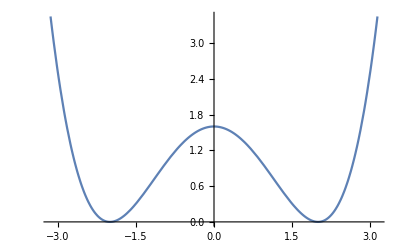

```mathematica
pot[x_]:=(x^2-4)^2/10
Plot[pot[x],{x,-π,π}]
```

```mathematica
(* set up the Levy alpha-stable SDE *)
α=1;
(* drift *)
(* f[x_] := Sin[x] *)
(* f[{x_,y_}]:={y,-Sin[x]}; *)
f[{x_,y_}]:={y,-pot'[x]}
(* constant diffusion *)
g=0.1;
```

```mathematica
Expand[pot[x]]
```

8/5-(4 x^2)/5+x^4/10

```mathematica
ntraj=45;
nsamp=1;
plots=Table[{},{i,ntraj}];
dt = 0.002;
ns = 4000;
tvec=Table[j*dt,{j,0,ns}];
For[traj=44,traj≤ntraj,traj+=1,
mcsol=Table[{0,0},ns+1];
mcsol[[1]]={0.5,0.0}; (* initial condition *)
For[i=1,i≤ns,i+=1,
dlvec=Flatten[{RandomVariate[StableDistribution[1,α,0.0,0.0,dt g],nsamp],
RandomVariate[StableDistribution[1,α,0.0,0.0,dt g],nsamp]}];
mcsol[[i+1]] =mcsol[[i]]+ (dt*f[mcsol[[i]]] +  dlvec);
];
fname=StringJoin["mcsoldblwell",ToString[traj],".csv"];
Print[fname];
Export[fname,mcsol];
plots[[traj]]=ListPlot[mcsol];
]
```

mcsoldblwell44.csv

mcsoldblwell45.csv

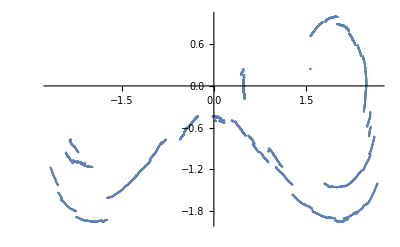

```mathematica
plots[[46]]
```

```mathematica
Export["mcsolgauss.csv",mcsol]
```

mcsolgauss.csv

```mathematica
StringJoin["mcsolgauss",ToString[2],".csv"]
```

mcsolgauss2.csv